## First - two masses and three strings

```mathematica
l1 = 1;
l12 = 2;
l2 = l1 + l12;
k =1;
```

```mathematica
solution = DSolve[{
x1''[t] == -k(x1[t] -l1) + k(x2[t]-x1[t]-l12),
x2''[t] == -k(x2[t] - l2) + k(x1[t] - x2[t] + l12),
x1[0] == 1,
x1'[0] == 0,
x2[0] == 2.7,
x2'[0] == 0
},
{x1[t], x2[t]}, t
]
```

{{x1[t]→2. (-0.075 Cos[t]+Cos[t]^2+0.075 Cos[√3 t]-0.5 Cos[√3 t]^2+Sin[t]^2-0.5 Sin[√3 t]^2),x2[t]→2. (-0.075 Cos[t]+Cos[t]^2-0.075 Cos[√3 t]+0.5 Cos[√3 t]^2+Sin[t]^2+0.5 Sin[√3 t]^2)}}

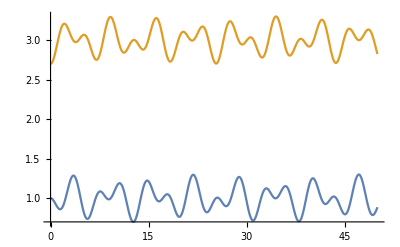

```mathematica
Plot[{solution[[1,1, 2]], solution[[1,2, 2]]}, {t, 0, 50}]
```